## “HDF5HighLevel Examples”

## Information

This file demonstrates some of the functionality of HDF5HighLevel examples.

Originally prepared 10 July 2011 by Scot Martin for Windows 7, 64-bit, Mathematica version 8.0.1 for the HDF5 technology of a DLL. Updated 12 August 2016 by Scot Martin for Windows 10, 64-bit, Mathematica version 11.0.0  switching to the new HDF5 technology of P/Invoke (https://www.hdfgroup.org/projects/hdf.net/).

The characteristic of being in the “high-level” package is that most functions operate directly on files (i.e., including opening and closing).

Email: scot_martin@harvard.edu.

## Set up

### Local Work Environment

Code last run on:

```mathematica
DateString[]
```

Thu 18 Aug 2016 18:31:28

```mathematica
$Version
```

11.0.0 for Microsoft Windows (64-bit) (July 28, 2016)

### Load Package

```mathematica
With[
{
packageFileName=
FileNameJoin[
{
ParentDirectory@NotebookDirectory[],
"HDF5.Mathematica.Packages",
"HDF5HighLevel.m"
}
]
},

Needs["HDF5HighLevel`",packageFileName]

]
```

```mathematica
$HDF5packageVersion
```

V2.0

```mathematica
H5BasicGetLibVersion[]
```

{1,8,17}

## Examples

### General Information

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
CompoundExpression[

Print["NamesAndTypes"],
Print[namesAndTypes=NamesAndTypes[filename]],

Print["\nDataSetsMetaData"],
Print[dataSetsMetaData=DataSetsMetaData[filename]],

numberOfDatasets=Replace["NumberOfDatasets",dataSetsMetaData],
namesOfDatasets=Replace["DatasetName",dataSetsMetaData],

Print["\nAttributes"],
Do[
With[{attributeName=namesOfDatasets⟦i⟧},
CompoundExpression[
Print["Attribute: ",attributeName],
Print[ReadAttributes[filename,attributeName,"ReturnValues"->True]]
]
],
{i,numberOfDatasets}
]
]
]
```

NamesAndTypes

{DATASET→{./Notes,./arrays/1D String,./arrays/2D float array,./arrays/2D int array,./arrays/2D int8x9,./arrays/3D int array,./arrays/4D int,./arrays/ArrayOfStructures,./arrays/Vdata with mixed types,./images/3D THG,./images/Iceberg,./images/hst_lagoon_detail.jpg,./images/iceberg_palette,./images/pixel interlace,./images/plane interlace},GROUP→{./arrays,./datatypes,./images},NAMED_DATATYPE→{./datatypes/H5T_NATIVE_INT}}

DataSetsMetaData

{NumberOfDatasets→15,DatasetName→{./Notes,./arrays/1D String,./arrays/2D float array,./arrays/2D int array,./arrays/2D int8x9,./arrays/3D int array,./arrays/4D int,./arrays/ArrayOfStructures,./arrays/Vdata with mixed types,./images/3D THG,./images/Iceberg,./images/hst_lagoon_detail.jpg,./images/iceberg_palette,./images/pixel interlace,./images/plane interlace},DatasetClassType→{STRING,STRING,FLOAT,INTEGER,INTEGER,INTEGER,INTEGER,COMPOUND,COMPOUND,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER},DatasetSystemType→{System.Byte[],System.Byte[],System.Single[],System.Int32[],System.Int32[],System.Int32[],System.Int32[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[]},DatasetSpaceDimensions→{{10,5},{1},{100,50},{100,50},{8,9},{100,50,10},{5,4,3,2},{3,10},{20},{8,72,144},{375,375},{610,600,3},{256,3},{149,227,3},{3,149,227}}}

Attributes

Attribute: ./Notes

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/1D String

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/2D float array

{NumberOfAttributes→1,AttributeName→{test},AttributeClassType→{STRING},AttributeSystemType→{System.Byte[]},AttributeSystemTypeCountInOneDatum→{10},AttributeSpaceDimensions→{{1}},AttributeValues→{test     }}

Attribute: ./arrays/2D int array

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/2D int8x9

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/3D int array

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/4D int

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/ArrayOfStructures

{NumberOfAttributes→0,AttributeName→{},AttributeClassType→{},AttributeSystemType→{},AttributeSystemTypeCountInOneDatum→{},AttributeSpaceDimensions→{},AttributeValues→{}}

Attribute: ./arrays/Vdata with mixed types

{NumberOfAttributes→3,AttributeName→{HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{22,5,1},AttributeSpaceDimensions→{{},{},{}},AttributeValues→{Vdata with mixed types,Vdata,46}}

Attribute: ./images/3D THG

{NumberOfAttributes→1,AttributeName→{CLASS},AttributeClassType→{STRING},AttributeSystemType→{System.Byte[]},AttributeSystemTypeCountInOneDatum→{7},AttributeSpaceDimensions→{{1}},AttributeValues→{IMAGE}}

Attribute: ./images/Iceberg

H5TExtendGetSystemTypeAndSize::badtype: Identified class of REFERENCE is not one of INTEGER, FLOAT, STRING, BITFIELD, ENUM, OPAQUE, COMPOUND, or ARRAY.

General::stop: Further output of H5TExtendGetSystemTypeAndSize::badtype will be suppressed during this calculation.

{NumberOfAttributes→6,AttributeName→{CLASS,IMAGE_COLORMODEL,IMAGE_MINMAXRANGE,IMAGE_SUBCLASS,IMAGE_VERSION,PALETTE},AttributeClassType→{STRING,STRING,INTEGER,STRING,FLOAT,REFERENCE},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Single[],Missing[NotSupported]},AttributeSystemTypeCountInOneDatum→{6,4,1,14,1,Missing[NotSupported]},AttributeSpaceDimensions→{{1},{1},{2},{1},{1},{1}},AttributeValues→{IMAGE,RGB,{0,255},IMAGE_INDEXED,1.,-1}}

Attribute: ./images/hst_lagoon_detail.jpg

{NumberOfAttributes→5,AttributeName→{CLASS,IMAGE_MINMAXRANGE,IMAGE_SUBCLASS,IMAGE_VERSION,INTERLACE_MODE},AttributeClassType→{STRING,INTEGER,STRING,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{6,1,16,4,16},AttributeSpaceDimensions→{{1},{2},{1},{1},{1}},AttributeValues→{IMAGE,{0,255},IMAGE_TRUECOLOR,1.2,INTERLACE_PIXEL}}

Attribute: ./images/iceberg_palette

{NumberOfAttributes→5,AttributeName→{CLASS,PAL_COLORMODEL,PAL_MINMAXNUMERIC,PAL_TYPE,PAL_VERSION},AttributeClassType→{STRING,STRING,INTEGER,STRING,FLOAT},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Single[]},AttributeSystemTypeCountInOneDatum→{8,4,1,12,1},AttributeSpaceDimensions→{{1},{1},{2},{1},{1}},AttributeValues→{PALETTE,RGB,{0,255},DIRECTINDEX,1.}}

Attribute: ./images/pixel interlace

{NumberOfAttributes→5,AttributeName→{CLASS,IMAGE_MINMAXRANGE,IMAGE_SUBCLASS,IMAGE_VERSION,INTERLACE_MODE},AttributeClassType→{STRING,INTEGER,STRING,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,1,16,4,15},AttributeSpaceDimensions→{{1},{2},{},{},{1}},AttributeValues→{IMAGE,{0,255},IMAGE_TRUECOLOR,1.2,INTERLACE_PIXEL}}

Attribute: ./images/plane interlace

{NumberOfAttributes→5,AttributeName→{CLASS,IMAGE_MINMAXRANGE,IMAGE_SUBCLASS,IMAGE_VERSION,INTERLACE_MODE},AttributeClassType→{STRING,INTEGER,STRING,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,1,16,3,15},AttributeSpaceDimensions→{{1},{2},{1},{1},{1}},AttributeValues→{IMAGE,{0,255},IMAGE_TRUECOLOR,1.2,INTERLACE_PLANE}}

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
ReadAttributes[filename,".","ReturnValues"->True]
]
```

{NumberOfAttributes→1,AttributeName→{test},AttributeClassType→{STRING},AttributeSystemType→{System.Byte[]},AttributeSystemTypeCountInOneDatum→{20},AttributeSpaceDimensions→{{1}},AttributeValues→{this is a test     }}

### Detailed information on a single compound datatype

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
CompoundDataTypeInformation[filename,"./arrays/ArrayOfStructures"]
]
```

{NumberOfMembers→4,MemberName→{a_name,c_name,b_name,nested_name},MemberClassType→{INTEGER,FLOAT,FLOAT,COMPOUND},MemberSystemType→{System.Int32[],System.Double[],System.Single[],System.Byte[]},MemberSystemTypeCountInOneDatum→{1,1,1,12}}

Above shows a compound data type within a compound data type. The function does not have enough versatility to dig down into the details of this next compound data type. Options: (1) The file would need to be opened and examined in detail using the basic and extended packages. See the intermediate tutorials. (2) Use the alternative function CompoundDataTypeInformationTree[ ] (see next section below).

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
CompoundDataTypeInformation[filename,"./arrays/Vdata with mixed types"]
]
```

{NumberOfMembers→7,MemberName→{Character,Short,Integer,Float,String,Integer Array,Float Array},MemberClassType→{STRING,INTEGER,INTEGER,FLOAT,STRING,ARRAY,ARRAY},MemberSystemType→{System.Byte[],System.Int16[],System.Int32[],System.Single[],System.Byte[],System.Int32[],System.Single[]},MemberSystemTypeCountInOneDatum→{1,1,1,1,10,{4},{20}}}

### Detailed information on a nested compound datatypes

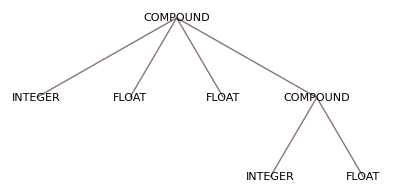

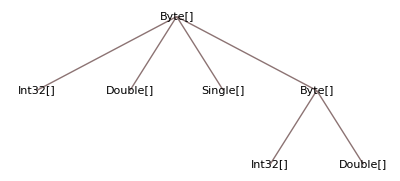

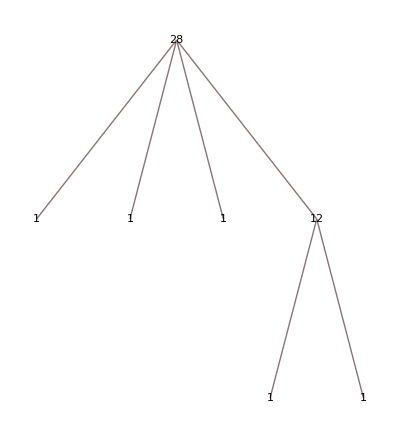

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
CompoundDataTypeInformationTree[filename,"./arrays/ArrayOfStructures"]
]
```

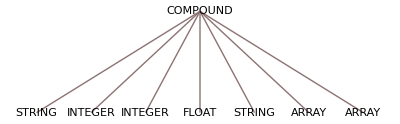

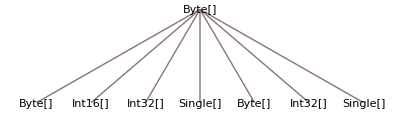

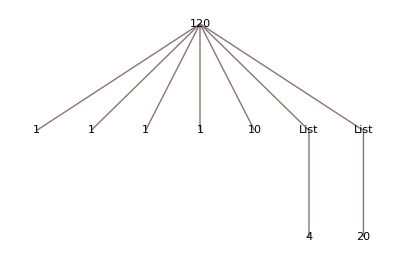

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
CompoundDataTypeInformationTree[filename,"./arrays/Vdata with mixed types"]
]
```

### Read Data

#### Strings

```mathematica
With[
{
filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]
},
ReadRank2[filename,"./Notes"]
] //TableForm
```

http://www.hdfgroup.org/ | http://www.hdfgroup.org/HDF5/ | http://www.hdfgroup.org/products/hdf4/ | http://www.hdfgroup.org/hdf-java-html/index.html | http://www.hdfgroup.org/products/
http://www.hdfgroup.org/hdf-java-html/hdfview/index.html | The HDFView is a Java-based tool for browsing and editing HDF4 a | Set the bounds of library versions | Use H5Ocopy() for copying datasets or groups (important for larg | view a file hierarchy in a tree structure 
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/index.h | HDFView allows users to browse through any HDF4 and HDF5 file | Set link creation order | Show and modify dangling links | create new file, add or delete groups and datasets 
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug01int | HDFView allows a user to descend through the hierarchy and navig | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug01int | The content of a data object is loaded only when the object is s | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug02sta | HDFView editing features allow a user to create, delete, and mod | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug03obj | The HDFView graphical user interface (GUI) is simple and easy-to | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug04tre | HDFView was implemented by using the JavaTM 2 Platform, which is | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug05spr | The GUI components have the same look-and-feel for all machines | test string | test string | test string
http://www.hdfgroup.org/hdf-java-html/hdfview/UsersGuide/ug06ima | HDFView uses conventional folders and icons to display groups an | test string | test string | test string

#### Full data and hyperslab

Full data

```mathematica
With[
{
filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]
},
ReadRank2[filename,"./arrays/2D float array"]
] //TableForm
```

0.000123457 | 0.0012345 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.9 | 1.7 | 2.6 | 3.5 | 4.4 | 5.2 | 6.1 | 7. | 7.8 | 8.7 | 9.6 | 10.5 | 11.3 | 12.2 | 13.1 | 13.9 | 14.8 | 15.6 | 16.5 | 17.4 | 18.2 | 19.1 | 19.9 | 20.8 | 21.6 | 22.5 | 23.3 | 24.2 | 25. | 25.9 | 26.7 | 27.6 | 28.4 | 29.2 | 30.1 | 30.9 | 31.7 | 32.6 | 33.4 | 34.2 | 35. | 35.8 | 36.7 | 37.5 | 38.3 | 39.1 | 39.9 | 40.7 | 41.5
0. | 1.7 | 3.5 | 5.2 | 7. | 8.7 | 10.5 | 12.2 | 13.9 | 15.6 | 17.4 | 19.1 | 20.8 | 22.5 | 24.2 | 25.9 | 27.6 | 29.2 | 30.9 | 32.6 | 34.2 | 35.8 | 37.5 | 39.1 | 40.7 | 42.3 | 43.8 | 45.4 | 46.9 | 48.5 | 50. | 51.5 | 53. | 54.5 | 55.9 | 57.4 | 58.8 | 60.2 | 61.6 | 62.9 | 64.3 | 65.6 | 66.9 | 68.2 | 69.5 | 70.7 | 71.9 | 73.1 | 74.3 | 75.5
0.17 | 2.6 | 3.5 | 7.8 | 10.5 | 13.1 | 15.6 | 18.2 | 20.8 | 23.3 | 25.9 | 28.4 | 30.9 | 33.4 | 35.8 | 38.3 | 40.7 | 43.1 | 45.4 | 47.7 | 50. | 52.2 | 54.5 | 56.6 | 58.8 | 60.9 | 62.9 | 64.9 | 66.9 | 68.8 | 70.7 | 72.5 | 74.3 | 76. | 77.7 | 79.3 | 80.9 | 82.4 | 83.9 | 85.3 | 86.6 | 87.9 | 89.1 | 90.3 | 91.4 | 92.4 | 93.4 | 94.3 | 95.1 | 95.9
0.35 | 5.2 | 7. | 10.5 | 13.9 | 17.4 | 20.8 | 24.2 | 27.6 | 30.9 | 34.2 | 37.5 | 40.7 | 43.8 | 46.9 | 50. | 53. | 55.9 | 58.8 | 61.6 | 64.3 | 66.9 | 69.5 | 71.9 | 74.3 | 76.6 | 78.8 | 80.9 | 82.9 | 84.8 | 86.6 | 88.3 | 89.9 | 91.4 | 92.7 | 94. | 95.1 | 96.1 | 97. | 97.8 | 98.5 | 99. | 99.5 | 99.8 | 99.9 | 100. | 99.9 | 99.8 | 99.5 | 99.
0.52 | 7.8 | 10.5 | 13.1 | 17.4 | 21.6 | 25.9 | 30.1 | 34.2 | 38.3 | 42.3 | 46.2 | 50. | 53.7 | 57.4 | 60.9 | 64.3 | 67.6 | 70.7 | 73.7 | 76.6 | 79.3 | 81.9 | 84.3 | 86.6 | 88.7 | 90.6 | 92.4 | 94. | 95.4 | 96.6 | 97.6 | 98.5 | 99.1 | 99.6 | 99.9 | 100. | 99.9 | 99.6 | 99.1 | 98.5 | 97.6 | 96.6 | 95.4 | 94. | 92.4 | 90.6 | 88.7 | 86.6 | 84.3
0.7 | 10.5 | 13.9 | 15.6 | 20.8 | 25.9 | 30.9 | 35.8 | 40.7 | 45.4 | 50. | 54.5 | 58.8 | 62.9 | 66.9 | 70.7 | 74.3 | 77.7 | 80.9 | 83.9 | 86.6 | 89.1 | 91.4 | 93.4 | 95.1 | 96.6 | 97.8 | 98.8 | 99.5 | 99.9 | 100. | 99.9 | 99.5 | 98.8 | 97.8 | 96.6 | 95.1 | 93.4 | 91.4 | 89.1 | 86.6 | 83.9 | 80.9 | 77.7 | 74.3 | 70.7 | 66.9 | 62.9 | 58.8 | 54.5
0.87 | 13.1 | 17.4 | 18.2 | 24.2 | 30.1 | 35.8 | 41.5 | 46.9 | 52.2 | 57.4 | 62.3 | 66.9 | 71.3 | 75.5 | 79.3 | 82.9 | 86.2 | 89.1 | 91.7 | 94. | 95.9 | 97.4 | 98.6 | 99.5 | 99.9 | 100. | 99.7 | 99. | 98. | 96.6 | 94.8 | 92.7 | 90.3 | 87.5 | 84.3 | 80.9 | 77.2 | 73.1 | 68.8 | 64.3 | 59.5 | 54.5 | 49.2 | 43.8 | 38.3 | 32.6 | 26.7 | 20.8 | 14.8
1.05 | 15.6 | 20.8 | 20.8 | 27.6 | 34.2 | 40.7 | 46.9 | 53. | 58.8 | 64.3 | 69.5 | 74.3 | 78.8 | 82.9 | 86.6 | 89.9 | 92.7 | 95.1 | 97. | 98.5 | 99.5 | 99.9 | 99.9 | 99.5 | 98.5 | 97. | 95.1 | 92.7 | 89.9 | 86.6 | 82.9 | 78.8 | 74.3 | 69.5 | 64.3 | 58.8 | 53. | 46.9 | 40.7 | 34.2 | 27.6 | 20.8 | 13.9 | 7. | 0. | -7. | -13.9 | -20.8 | -27.6
1.22 | 18.2 | 24.2 | 23.3 | 30.9 | 38.3 | 45.4 | 52.2 | 58.8 | 64.9 | 70.7 | 76. | 80.9 | 85.3 | 89.1 | 92.4 | 95.1 | 97.2 | 98.8 | 99.7 | 100. | 99.7 | 98.8 | 97.2 | 95.1 | 92.4 | 89.1 | 85.3 | 80.9 | 76. | 70.7 | 64.9 | 58.8 | 52.2 | 45.4 | 38.3 | 30.9 | 23.3 | 15.6 | 7.8 | 0. | -7.8 | -15.6 | -23.3 | -30.9 | -38.3 | -45.4 | -52.2 | -58.8 | -64.9
1.39 | 20.8 | 27.6 | 25.9 | 34.2 | 42.3 | 50. | 57.4 | 64.3 | 70.7 | 76.6 | 81.9 | 86.6 | 90.6 | 94. | 96.6 | 98.5 | 99.6 | 100. | 99.6 | 98.5 | 96.6 | 94. | 90.6 | 86.6 | 81.9 | 76.6 | 70.7 | 64.3 | 57.4 | 50. | 42.3 | 34.2 | 25.9 | 17.4 | 8.7 | 0. | -8.7 | -17.4 | -25.9 | -34.2 | -42.3 | -50. | -57.4 | -64.3 | -70.7 | -76.6 | -81.9 | -86.6 | -90.6
1.56 | 23.3 | 30.9 | 28.4 | 37.5 | 46.2 | 54.5 | 62.3 | 69.5 | 76. | 81.9 | 87. | 91.4 | 94.8 | 97.4 | 99.1 | 99.9 | 99.8 | 98.8 | 96.8 | 94. | 90.3 | 85.7 | 80.4 | 74.3 | 67.6 | 60.2 | 52.2 | 43.8 | 35. | 25.9 | 16.5 | 7. | -2.6 | -12.2 | -21.6 | -30.9 | -39.9 | -48.5 | -56.6 | -64.3 | -71.3 | -77.7 | -83.4 | -88.3 | -92.4 | -95.6 | -98. | -99.5 | -100.
1.74 | 25.9 | 34.2 | 30.9 | 40.7 | 50. | 58.8 | 66.9 | 74.3 | 80.9 | 86.6 | 91.4 | 95.1 | 97.8 | 99.5 | 100. | 99.5 | 97.8 | 95.1 | 91.4 | 86.6 | 80.9 | 74.3 | 66.9 | 58.8 | 50. | 40.7 | 30.9 | 20.8 | 10.5 | 0. | -10.5 | -20.8 | -30.9 | -40.7 | -50. | -58.8 | -66.9 | -74.3 | -80.9 | -86.6 | -91.4 | -95.1 | -97.8 | -99.5 | -100. | -99.5 | -97.8 | -95.1 | -91.4
1.91 | 28.4 | 37.5 | 33.4 | 43.8 | 53.7 | 62.9 | 71.3 | 78.8 | 85.3 | 90.6 | 94.8 | 97.8 | 99.5 | 100. | 99.1 | 97. | 93.7 | 89.1 | 83.4 | 76.6 | 68.8 | 60.2 | 50.8 | 40.7 | 30.1 | 19.1 | 7.8 | -3.5 | -14.8 | -25.9 | -36.7 | -46.9 | -56.6 | -65.6 | -73.7 | -80.9 | -87. | -92.1 | -95.9 | -98.5 | -99.8 | -99.9 | -98.6 | -96.1 | -92.4 | -87.5 | -81.4 | -74.3 | -66.3
2.08 | 30.9 | 40.7 | 35.8 | 46.9 | 57.4 | 66.9 | 75.5 | 82.9 | 89.1 | 94. | 97.4 | 99.5 | 100. | 99. | 96.6 | 92.7 | 87.5 | 80.9 | 73.1 | 64.3 | 54.5 | 43.8 | 32.6 | 20.8 | 8.7 | -3.5 | -15.6 | -27.6 | -39.1 | -50. | -60.2 | -69.5 | -77.7 | -84.8 | -90.6 | -95.1 | -98.2 | -99.8 | -99.9 | -98.5 | -95.6 | -91.4 | -85.7 | -78.8 | -70.7 | -61.6 | -51.5 | -40.7 | -29.2
2.25 | 33.4 | 43.8 | 38.3 | 50. | 60.9 | 70.7 | 79.3 | 86.6 | 92.4 | 96.6 | 99.1 | 100. | 99.1 | 96.6 | 92.4 | 86.6 | 79.3 | 70.7 | 60.9 | 50. | 38.3 | 25.9 | 13.1 | 0. | -13.1 | -25.9 | -38.3 | -50. | -60.9 | -70.7 | -79.3 | -86.6 | -92.4 | -96.6 | -99.1 | -100. | -99.1 | -96.6 | -92.4 | -86.6 | -79.3 | -70.7 | -60.9 | -50. | -38.3 | -25.9 | -13.1 | 0. | 13.1
2.42 | 35.8 | 46.9 | 40.7 | 53. | 64.3 | 74.3 | 82.9 | 89.9 | 95.1 | 98.5 | 99.9 | 99.5 | 97. | 92.7 | 86.6 | 78.8 | 69.5 | 58.8 | 46.9 | 34.2 | 20.8 | 7. | -7. | -20.8 | -34.2 | -46.9 | -58.8 | -69.5 | -78.8 | -86.6 | -92.7 | -97. | -99.5 | -99.9 | -98.5 | -95.1 | -89.9 | -82.9 | -74.3 | -64.3 | -53. | -40.7 | -27.6 | -13.9 | 0. | 13.9 | 27.6 | 40.7 | 53.
2.59 | 38.3 | 50. | 43.1 | 55.9 | 67.6 | 77.7 | 86.2 | 92.7 | 97.2 | 99.6 | 99.8 | 97.8 | 93.7 | 87.5 | 79.3 | 69.5 | 58.1 | 45.4 | 31.7 | 17.4 | 2.6 | -12.2 | -26.7 | -40.7 | -53.7 | -65.6 | -76. | -84.8 | -91.7 | -96.6 | -99.4 | -99.9 | -98.3 | -94.6 | -88.7 | -80.9 | -71.3 | -60.2 | -47.7 | -34.2 | -19.9 | -5.2 | 9.6 | 24.2 | 38.3 | 51.5 | 63.6 | 74.3 | 83.4
2.76 | 40.7 | 53. | 45.4 | 58.8 | 70.7 | 80.9 | 89.1 | 95.1 | 98.8 | 100. | 98.8 | 95.1 | 89.1 | 80.9 | 70.7 | 58.8 | 45.4 | 30.9 | 15.6 | 0. | -15.6 | -30.9 | -45.4 | -58.8 | -70.7 | -80.9 | -89.1 | -95.1 | -98.8 | -100. | -98.8 | -95.1 | -89.1 | -80.9 | -70.7 | -58.8 | -45.4 | -30.9 | -15.6 | 0. | 15.6 | 30.9 | 45.4 | 58.8 | 70.7 | 80.9 | 89.1 | 95.1 | 98.8
0. | 16.5 | 32.6 | 47.7 | 61.6 | 73.7 | 83.9 | 91.7 | 97. | 99.7 | 99.6 | 96.8 | 91.4 | 83.4 | 73.1 | 60.9 | 46.9 | 31.7 | 15.6 | -0.9 | -17.4 | -33.4 | -48.5 | -62.3 | -74.3 | -84.3 | -92.1 | -97.2 | -99.8 | -99.5 | -96.6 | -91. | -82.9 | -72.5 | -60.2 | -46.2 | -30.9 | -14.8 | 1.7 | 18.2 | 34.2 | 49.2 | 62.9 | 74.9 | 84.8 | 92.4 | 97.4 | 99.8 | 99.5 | 96.4
0. | 17.4 | 34.2 | 50. | 64.3 | 76.6 | 86.6 | 94. | 98.5 | 100. | 98.5 | 94. | 86.6 | 76.6 | 64.3 | 50. | 34.2 | 17.4 | 0. | -17.4 | -34.2 | -50. | -64.3 | -76.6 | -86.6 | -94. | -98.5 | -100. | -98.5 | -94. | -86.6 | -76.6 | -64.3 | -50. | -34.2 | -17.4 | 0. | 17.4 | 34.2 | 50. | 64.3 | 76.6 | 86.6 | 94. | 98.5 | 100. | 98.5 | 94. | 86.6 | 76.6
0. | 18.2 | 35.8 | 52.2 | 66.9 | 79.3 | 89.1 | 95.9 | 99.5 | 99.7 | 96.6 | 90.3 | 80.9 | 68.8 | 54.5 | 38.3 | 20.8 | 2.6 | -15.6 | -33.4 | -50. | -64.9 | -77.7 | -87.9 | -95.1 | -99.1 | -99.9 | -97.2 | -91.4 | -82.4 | -70.7 | -56.6 | -40.7 | -23.3 | -5.2 | 13.1 | 30.9 | 47.7 | 62.9 | 76. | 86.6 | 94.3 | 98.8 | 100. | 97.8 | 92.4 | 83.9 | 72.5 | 58.8 | 43.1
0. | 19.1 | 37.5 | 54.5 | 69.5 | 81.9 | 91.4 | 97.4 | 99.9 | 98.8 | 94. | 85.7 | 74.3 | 60.2 | 43.8 | 25.9 | 7. | -12.2 | -30.9 | -48.5 | -64.3 | -77.7 | -88.3 | -95.6 | -99.5 | -99.6 | -96.1 | -89.1 | -78.8 | -65.6 | -50. | -32.6 | -13.9 | 5.2 | 24.2 | 42.3 | 58.8 | 73.1 | 84.8 | 93.4 | 98.5 | 100. | 97.8 | 92.1 | 82.9 | 70.7 | 55.9 | 39.1 | 20.8 | 1.7
0. | 19.9 | 39.1 | 56.6 | 71.9 | 84.3 | 93.4 | 98.6 | 99.9 | 97.2 | 90.6 | 80.4 | 66.9 | 50.8 | 32.6 | 13.1 | -7. | -26.7 | -45.4 | -62.3 | -76.6 | -87.9 | -95.6 | -99.5 | -99.5 | -95.4 | -87.5 | -76. | -61.6 | -44.6 | -25.9 | -6.1 | 13.9 | 33.4 | 51.5 | 67.6 | 80.9 | 91. | 97.4 | 100. | 98.5 | 93. | 83.9 | 71.3 | 55.9 | 38.3 | 19.1 | -0.9 | -20.8 | -39.9
0. | 20.8 | 40.7 | 58.8 | 74.3 | 86.6 | 95.1 | 99.5 | 99.5 | 95.1 | 86.6 | 74.3 | 58.8 | 40.7 | 20.8 | 0. | -20.8 | -40.7 | -58.8 | -74.3 | -86.6 | -95.1 | -99.5 | -99.5 | -95.1 | -86.6 | -74.3 | -58.8 | -40.7 | -20.8 | 0. | 20.8 | 40.7 | 58.8 | 74.3 | 86.6 | 95.1 | 99.5 | 99.5 | 95.1 | 86.6 | 74.3 | 58.8 | 40.7 | 20.8 | 0. | -20.8 | -40.7 | -58.8 | -74.3
0. | 21.6 | 42.3 | 60.9 | 76.6 | 88.7 | 96.6 | 99.9 | 98.5 | 92.4 | 81.9 | 67.6 | 50. | 30.1 | 8.7 | -13.1 | -34.2 | -53.7 | -70.7 | -84.3 | -94. | -99.1 | -99.6 | -95.4 | -86.6 | -73.7 | -57.4 | -38.3 | -17.4 | 4.4 | 25.9 | 46.2 | 64.3 | 79.3 | 90.6 | 97.6 | 100. | 97.6 | 90.6 | 79.3 | 64.3 | 46.2 | 25.9 | 4.4 | -17.4 | -38.3 | -57.4 | -73.7 | -86.6 | -95.4
0. | 22.5 | 43.8 | 62.9 | 78.8 | 90.6 | 97.8 | 100. | 97. | 89.1 | 76.6 | 60.2 | 40.7 | 19.1 | -3.5 | -25.9 | -46.9 | -65.6 | -80.9 | -92.1 | -98.5 | -99.9 | -96.1 | -87.5 | -74.3 | -57.4 | -37.5 | -15.6 | 7. | 29.2 | 50. | 68.2 | 82.9 | 93.4 | 99. | 99.6 | 95.1 | 85.7 | 71.9 | 54.5 | 34.2 | 12.2 | -10.5 | -32.6 | -53. | -70.7 | -84.8 | -94.6 | -99.5 | -99.3
0. | 23.3 | 45.4 | 64.9 | 80.9 | 92.4 | 98.8 | 99.7 | 95.1 | 85.3 | 70.7 | 52.2 | 30.9 | 7.8 | -15.6 | -38.3 | -58.8 | -76. | -89.1 | -97.2 | -100. | -97.2 | -89.1 | -76. | -58.8 | -38.3 | -15.6 | 7.8 | 30.9 | 52.2 | 70.7 | 85.3 | 95.1 | 99.7 | 98.8 | 92.4 | 80.9 | 64.9 | 45.4 | 23.3 | 0. | -23.3 | -45.4 | -64.9 | -80.9 | -92.4 | -98.8 | -99.7 | -95.1 | -85.3
0. | 24.2 | 46.9 | 66.9 | 82.9 | 94. | 99.5 | 99. | 92.7 | 80.9 | 64.3 | 43.8 | 20.8 | -3.5 | -27.6 | -50. | -69.5 | -84.8 | -95.1 | -99.8 | -98.5 | -91.4 | -78.8 | -61.6 | -40.7 | -17.4 | 7. | 30.9 | 53. | 71.9 | 86.6 | 96.1 | 99.9 | 97.8 | 89.9 | 76.6 | 58.8 | 37.5 | 13.9 | -10.5 | -34.2 | -55.9 | -74.3 | -88.3 | -97. | -100. | -97. | -88.3 | -74.3 | -55.9
0. | 25. | 48.5 | 68.8 | 84.8 | 95.4 | 99.9 | 98. | 89.9 | 76. | 57.4 | 35. | 10.5 | -14.8 | -39.1 | -60.9 | -78.8 | -91.7 | -98.8 | -99.5 | -94. | -82.4 | -65.6 | -44.6 | -20.8 | 4.4 | 29.2 | 52.2 | 71.9 | 87. | 96.6 | 100. | 97. | 87.9 | 73.1 | 53.7 | 30.9 | 6.1 | -19.1 | -43.1 | -64.3 | -81.4 | -93.4 | -99.4 | -99. | -92.4 | -79.9 | -62.3 | -40.7 | -16.5
0. | 25.9 | 50. | 70.7 | 86.6 | 96.6 | 100. | 96.6 | 86.6 | 70.7 | 50. | 25.9 | 0. | -25.9 | -50. | -70.7 | -86.6 | -96.6 | -100. | -96.6 | -86.6 | -70.7 | -50. | -25.9 | 0. | 25.9 | 50. | 70.7 | 86.6 | 96.6 | 100. | 96.6 | 86.6 | 70.7 | 50. | 25.9 | 0. | -25.9 | -50. | -70.7 | -86.6 | -96.6 | -100. | -96.6 | -86.6 | -70.7 | -50. | -25.9 | 0. | 25.9
0. | 26.7 | 51.5 | 72.5 | 88.3 | 97.6 | 99.9 | 94.8 | 82.9 | 64.9 | 42.3 | 16.5 | -10.5 | -36.7 | -60.2 | -79.3 | -92.7 | -99.4 | -98.8 | -91. | -76.6 | -56.6 | -32.6 | -6.1 | 20.8 | 46.2 | 68.2 | 85.3 | 96.1 | 100. | 96.6 | 86.2 | 69.5 | 47.7 | 22.5 | -4.4 | -30.9 | -55.2 | -75.5 | -90.3 | -98.5 | -99.5 | -93.4 | -80.4 | -61.6 | -38.3 | -12.2 | 14.8 | 40.7 | 63.6
0. | 27.6 | 53. | 74.3 | 89.9 | 98.5 | 99.5 | 92.7 | 78.8 | 58.8 | 34.2 | 7. | -20.8 | -46.9 | -69.5 | -86.6 | -97. | -99.9 | -95.1 | -82.9 | -64.3 | -40.7 | -13.9 | 13.9 | 40.7 | 64.3 | 82.9 | 95.1 | 99.9 | 97. | 86.6 | 69.5 | 46.9 | 20.8 | -7. | -34.2 | -58.8 | -78.8 | -92.7 | -99.5 | -98.5 | -89.9 | -74.3 | -53. | -27.6 | 0. | 27.6 | 53. | 74.3 | 89.9
0. | 28.4 | 54.5 | 76. | 91.4 | 99.1 | 98.8 | 90.3 | 74.3 | 52.2 | 25.9 | -2.6 | -30.9 | -56.6 | -77.7 | -92.4 | -99.5 | -98.3 | -89.1 | -72.5 | -50. | -23.3 | 5.2 | 33.4 | 58.8 | 79.3 | 93.4 | 99.7 | 97.8 | 87.9 | 70.7 | 47.7 | 20.8 | -7.8 | -35.8 | -60.9 | -80.9 | -94.3 | -99.9 | -97.2 | -86.6 | -68.8 | -45.4 | -18.2 | 10.5 | 38.3 | 62.9 | 82.4 | 95.1 | 100.
0. | 29.2 | 55.9 | 77.7 | 92.7 | 99.6 | 97.8 | 87.5 | 69.5 | 45.4 | 17.4 | -12.2 | -40.7 | -65.6 | -84.8 | -96.6 | -99.9 | -94.6 | -80.9 | -60.2 | -34.2 | -5.2 | 24.2 | 51.5 | 74.3 | 90.6 | 99. | 98.8 | 89.9 | 73.1 | 50. | 22.5 | -7. | -35.8 | -61.6 | -81.9 | -95.1 | -100. | -96.1 | -83.9 | -64.3 | -39.1 | -10.5 | 19.1 | 46.9 | 70.7 | 88.3 | 98.2 | 99.5 | 92.1
0. | 30.1 | 57.4 | 79.3 | 94. | 99.9 | 96.6 | 84.3 | 64.3 | 38.3 | 8.7 | -21.6 | -50. | -73.7 | -90.6 | -99.1 | -98.5 | -88.7 | -70.7 | -46.2 | -17.4 | 13.1 | 42.3 | 67.6 | 86.6 | 97.6 | 99.6 | 92.4 | 76.6 | 53.7 | 25.9 | -4.4 | -34.2 | -60.9 | -81.9 | -95.4 | -100. | -95.4 | -81.9 | -60.9 | -34.2 | -4.4 | 25.9 | 53.7 | 76.6 | 92.4 | 99.6 | 97.6 | 86.6 | 67.6
0. | 30.9 | 58.8 | 80.9 | 95.1 | 100. | 95.1 | 80.9 | 58.8 | 30.9 | 0. | -30.9 | -58.8 | -80.9 | -95.1 | -100. | -95.1 | -80.9 | -58.8 | -30.9 | 0. | 30.9 | 58.8 | 80.9 | 95.1 | 100. | 95.1 | 80.9 | 58.8 | 30.9 | 0. | -30.9 | -58.8 | -80.9 | -95.1 | -100. | -95.1 | -80.9 | -58.8 | -30.9 | 0. | 30.9 | 58.8 | 80.9 | 95.1 | 100. | 95.1 | 80.9 | 58.8 | 30.9
0. | 31.7 | 60.2 | 82.4 | 96.1 | 99.9 | 93.4 | 77.2 | 53. | 23.3 | -8.7 | -39.9 | -66.9 | -87. | -98.2 | -99.1 | -89.9 | -71.3 | -45.4 | -14.8 | 17.4 | 47.7 | 73.1 | 91. | 99.5 | 97.6 | 85.7 | 64.9 | 37.5 | 6.1 | -25.9 | -55.2 | -78.8 | -94.3 | -100. | -95.4 | -80.9 | -58.1 | -29.2 | 2.6 | 34.2 | 62.3 | 83.9 | 96.8 | 99.8 | 92.4 | 75.5 | 50.8 | 20.8 | -11.3
0. | 32.6 | 61.6 | 83.9 | 97. | 99.6 | 91.4 | 73.1 | 46.9 | 15.6 | -17.4 | -48.5 | -74.3 | -92.1 | -99.8 | -96.6 | -82.9 | -60.2 | -30.9 | 1.7 | 34.2 | 62.9 | 84.8 | 97.4 | 99.5 | 90.6 | 71.9 | 45.4 | 13.9 | -19.1 | -50. | -75.5 | -92.7 | -99.9 | -96.1 | -81.9 | -58.8 | -29.2 | 3.5 | 35.8 | 64.3 | 85.7 | 97.8 | 99.3 | 89.9 | 70.7 | 43.8 | 12.2 | -20.8 | -51.5
0. | 33.4 | 62.9 | 85.3 | 97.8 | 99.1 | 89.1 | 68.8 | 40.7 | 7.8 | -25.9 | -56.6 | -80.9 | -95.9 | -99.9 | -92.4 | -74.3 | -47.7 | -15.6 | 18.2 | 50. | 76. | 93.4 | 100. | 95.1 | 79.3 | 54.5 | 23.3 | -10.5 | -43.1 | -70.7 | -90.3 | -99.5 | -97.2 | -83.9 | -60.9 | -30.9 | 2.6 | 35.8 | 64.9 | 86.6 | 98.3 | 98.8 | 87.9 | 66.9 | 38.3 | 5.2 | -28.4 | -58.8 | -82.4
0. | 34.2 | 64.3 | 86.6 | 98.5 | 98.5 | 86.6 | 64.3 | 34.2 | 0. | -34.2 | -64.3 | -86.6 | -98.5 | -98.5 | -86.6 | -64.3 | -34.2 | 0. | 34.2 | 64.3 | 86.6 | 98.5 | 98.5 | 86.6 | 64.3 | 34.2 | 0. | -34.2 | -64.3 | -86.6 | -98.5 | -98.5 | -86.6 | -64.3 | -34.2 | 0. | 34.2 | 64.3 | 86.6 | 98.5 | 98.5 | 86.6 | 64.3 | 34.2 | 0. | -34.2 | -64.3 | -86.6 | -98.5
0. | 35. | 65.6 | 87.9 | 99. | 97.6 | 83.9 | 59.5 | 27.6 | -7.8 | -42.3 | -71.3 | -91.4 | -99.8 | -95.6 | -79.3 | -53. | -19.9 | 15.6 | 49.2 | 76.6 | 94.3 | 100. | 93. | 74.3 | 46.2 | 12.2 | -23.3 | -55.9 | -81.4 | -96.6 | -99.5 | -89.9 | -68.8 | -39.1 | -4.4 | 30.9 | 62.3 | 85.7 | 98.3 | 98.5 | 86.2 | 62.9 | 31.7 | -3.5 | -38.3 | -68.2 | -89.5 | -99.5 | -96.8
0. | 35.8 | 66.9 | 89.1 | 99.5 | 96.6 | 80.9 | 54.5 | 20.8 | -15.6 | -50. | -77.7 | -95.1 | -99.9 | -91.4 | -70.7 | -40.7 | -5.2 | 30.9 | 62.9 | 86.6 | 98.8 | 97.8 | 83.9 | 58.8 | 25.9 | -10.5 | -45.4 | -74.3 | -93.4 | -100. | -93.4 | -74.3 | -45.4 | -10.5 | 25.9 | 58.8 | 83.9 | 97.8 | 98.8 | 86.6 | 62.9 | 30.9 | -5.2 | -40.7 | -70.7 | -91.4 | -99.9 | -95.1 | -77.7
0. | 36.7 | 68.2 | 90.3 | 99.8 | 95.4 | 77.7 | 49.2 | 13.9 | -23.3 | -57.4 | -83.4 | -97.8 | -98.6 | -85.7 | -60.9 | -27.6 | 9.6 | 45.4 | 74.9 | 94. | 100. | 92.1 | 71.3 | 40.7 | 4.4 | -32.6 | -64.9 | -88.3 | -99.4 | -96.6 | -80.4 | -53. | -18.2 | 19.1 | 53.7 | 80.9 | 96.8 | 99.3 | 87.9 | 64.3 | 31.7 | -5.2 | -41.5 | -71.9 | -92.4 | -100. | -93.7 | -74.3 | -44.6
0. | 37.5 | 69.5 | 91.4 | 99.9 | 94. | 74.3 | 43.8 | 7. | -30.9 | -64.3 | -88.3 | -99.5 | -96.1 | -78.8 | -50. | -13.9 | 24.2 | 58.8 | 84.8 | 98.5 | 97.8 | 82.9 | 55.9 | 20.8 | -17.4 | -53. | -80.9 | -97. | -99. | -86.6 | -61.6 | -27.6 | 10.5 | 46.9 | 76.6 | 95.1 | 99.8 | 89.9 | 66.9 | 34.2 | -3.5 | -40.7 | -71.9 | -92.7 | -100. | -92.7 | -71.9 | -40.7 | -3.5
0. | 38.3 | 70.7 | 92.4 | 100. | 92.4 | 70.7 | 38.3 | 0. | -38.3 | -70.7 | -92.4 | -100. | -92.4 | -70.7 | -38.3 | 0. | 38.3 | 70.7 | 92.4 | 100. | 92.4 | 70.7 | 38.3 | 0. | -38.3 | -70.7 | -92.4 | -100. | -92.4 | -70.7 | -38.3 | 0. | 38.3 | 70.7 | 92.4 | 100. | 92.4 | 70.7 | 38.3 | 0. | -38.3 | -70.7 | -92.4 | -100. | -92.4 | -70.7 | -38.3 | 0. | 38.3
0. | 39.1 | 71.9 | 93.4 | 99.9 | 90.6 | 66.9 | 32.6 | -7. | -45.4 | -76.6 | -95.6 | -99.5 | -87.5 | -61.6 | -25.9 | 13.9 | 51.5 | 80.9 | 97.4 | 98.5 | 83.9 | 55.9 | 19.1 | -20.8 | -57.4 | -84.8 | -98.8 | -97. | -79.9 | -50. | -12.2 | 27.6 | 62.9 | 88.3 | 99.6 | 95.1 | 75.5 | 43.8 | 5.2 | -34.2 | -68.2 | -91.4 | -100. | -92.7 | -70.7 | -37.5 | 1.7 | 40.7 | 73.1
0. | 39.9 | 73.1 | 94.3 | 99.8 | 88.7 | 62.9 | 26.7 | -13.9 | -52.2 | -81.9 | -98. | -97.8 | -81.4 | -51.5 | -13.1 | 27.6 | 63.6 | 89.1 | 99.8 | 94. | 72.5 | 39.1 | -0.9 | -40.7 | -73.7 | -94.6 | -99.7 | -88.3 | -62.3 | -25.9 | 14.8 | 53. | 82.4 | 98.2 | 97.6 | 80.9 | 50.8 | 12.2 | -28.4 | -64.3 | -89.5 | -99.9 | -93.7 | -71.9 | -38.3 | 1.7 | 41.5 | 74.3 | 94.8
0. | 40.7 | 74.3 | 95.1 | 99.5 | 86.6 | 58.8 | 20.8 | -20.8 | -58.8 | -86.6 | -99.5 | -95.1 | -74.3 | -40.7 | 0. | 40.7 | 74.3 | 95.1 | 99.5 | 86.6 | 58.8 | 20.8 | -20.8 | -58.8 | -86.6 | -99.5 | -95.1 | -74.3 | -40.7 | 0. | 40.7 | 74.3 | 95.1 | 99.5 | 86.6 | 58.8 | 20.8 | -20.8 | -58.8 | -86.6 | -99.5 | -95.1 | -74.3 | -40.7 | 0. | 40.7 | 74.3 | 95.1 | 99.5
0. | 41.5 | 75.5 | 95.9 | 99. | 84.3 | 54.5 | 14.8 | -27.6 | -64.9 | -90.6 | -100. | -91.4 | -66.3 | -29.2 | 13.1 | 53. | 83.4 | 98.8 | 96.4 | 76.6 | 43.1 | 1.7 | -39.9 | -74.3 | -95.4 | -99.3 | -85.3 | -55.9 | -16.5 | 25.9 | 63.6 | 89.9 | 100. | 92.1 | 67.6 | 30.9 | -11.3 | -51.5 | -82.4 | -98.5 | -96.8 | -77.7 | -44.6 | -3.5 | 38.3 | 73.1 | 94.8 | 99.5 | 86.2
0. | 42.3 | 76.6 | 96.6 | 98.5 | 81.9 | 50. | 8.7 | -34.2 | -70.7 | -94. | -99.6 | -86.6 | -57.4 | -17.4 | 25.9 | 64.3 | 90.6 | 100. | 90.6 | 64.3 | 25.9 | -17.4 | -57.4 | -86.6 | -99.6 | -94. | -70.7 | -34.2 | 8.7 | 50. | 81.9 | 98.5 | 96.6 | 76.6 | 42.3 | 0. | -42.3 | -76.6 | -96.6 | -98.5 | -81.9 | -50. | -8.7 | 34.2 | 70.7 | 94. | 99.6 | 86.6 | 57.4
0. | 43.1 | 77.7 | 97.2 | 97.8 | 79.3 | 45.4 | 2.6 | -40.7 | -76. | -96.6 | -98.3 | -80.9 | -47.7 | -5.2 | 38.3 | 74.3 | 95.9 | 98.8 | 82.4 | 50. | 7.8 | -35.8 | -72.5 | -95.1 | -99.1 | -83.9 | -52.2 | -10.5 | 33.4 | 70.7 | 94.3 | 99.5 | 85.3 | 54.5 | 13.1 | -30.9 | -68.8 | -93.4 | -99.7 | -86.6 | -56.6 | -15.6 | 28.4 | 66.9 | 92.4 | 99.9 | 87.9 | 58.8 | 18.2
0. | 43.8 | 78.8 | 97.8 | 97. | 76.6 | 40.7 | -3.5 | -46.9 | -80.9 | -98.5 | -96.1 | -74.3 | -37.5 | 7. | 50. | 82.9 | 99. | 95.1 | 71.9 | 34.2 | -10.5 | -53. | -84.8 | -99.5 | -94. | -69.5 | -30.9 | 13.9 | 55.9 | 86.6 | 99.8 | 92.7 | 66.9 | 27.6 | -17.4 | -58.8 | -88.3 | -99.9 | -91.4 | -64.3 | -24.2 | 20.8 | 61.6 | 89.9 | 100. | 89.9 | 61.6 | 20.8 | -24.2
0. | 44.6 | 79.9 | 98.3 | 96.1 | 73.7 | 35.8 | -9.6 | -53. | -85.3 | -99.6 | -93. | -66.9 | -26.7 | 19.1 | 60.9 | 89.9 | 100. | 89.1 | 59.5 | 17.4 | -28.4 | -68.2 | -93.7 | -99.5 | -84.3 | -51.5 | -7.8 | 37.5 | 74.9 | 96.6 | 98. | 78.8 | 43.1 | -1.7 | -46.2 | -80.9 | -98.6 | -95.6 | -72.5 | -34.2 | 11.3 | 54.5 | 86.2 | 99.8 | 92.4 | 65.6 | 25. | -20.8 | -62.3
0. | 45.4 | 80.9 | 98.8 | 95.1 | 70.7 | 30.9 | -15.6 | -58.8 | -89.1 | -100. | -89.1 | -58.8 | -15.6 | 30.9 | 70.7 | 95.1 | 98.8 | 80.9 | 45.4 | 0. | -45.4 | -80.9 | -98.8 | -95.1 | -70.7 | -30.9 | 15.6 | 58.8 | 89.1 | 100. | 89.1 | 58.8 | 15.6 | -30.9 | -70.7 | -95.1 | -98.8 | -80.9 | -45.4 | 0. | 45.4 | 80.9 | 98.8 | 95.1 | 70.7 | 30.9 | -15.6 | -58.8 | -89.1
0. | 46.2 | 81.9 | 99.1 | 94. | 67.6 | 25.9 | -21.6 | -64.3 | -92.4 | -99.6 | -84.3 | -50. | -4.4 | 42.3 | 79.3 | 98.5 | 95.4 | 70.7 | 30.1 | -17.4 | -60.9 | -90.6 | -99.9 | -86.6 | -53.7 | -8.7 | 38.3 | 76.6 | 97.6 | 96.6 | 73.7 | 34.2 | -13.1 | -57.4 | -88.7 | -100. | -88.7 | -57.4 | -13.1 | 34.2 | 73.7 | 96.6 | 97.6 | 76.6 | 38.3 | -8.7 | -53.7 | -86.6 | -99.9
0. | 46.9 | 82.9 | 99.5 | 92.7 | 64.3 | 20.8 | -27.6 | -69.5 | -95.1 | -98.5 | -78.8 | -40.7 | 7. | 53. | 86.6 | 99.9 | 89.9 | 58.8 | 13.9 | -34.2 | -74.3 | -97. | -97. | -74.3 | -34.2 | 13.9 | 58.8 | 89.9 | 99.9 | 86.6 | 53. | 7. | -40.7 | -78.8 | -98.5 | -95.1 | -69.5 | -27.6 | 20.8 | 64.3 | 92.7 | 99.5 | 82.9 | 46.9 | 0. | -46.9 | -82.9 | -99.5 | -92.7
0. | 47.7 | 83.9 | 99.7 | 91.4 | 60.9 | 15.6 | -33.4 | -74.3 | -97.2 | -96.6 | -72.5 | -30.9 | 18.2 | 62.9 | 92.4 | 99.5 | 82.4 | 45.4 | -2.6 | -50. | -85.3 | -99.9 | -90.3 | -58.8 | -13.1 | 35.8 | 76. | 97.8 | 95.9 | 70.7 | 28.4 | -20.8 | -64.9 | -93.4 | -99.1 | -80.9 | -43.1 | 5.2 | 52.2 | 86.6 | 100. | 89.1 | 56.6 | 10.5 | -38.3 | -77.7 | -98.3 | -95.1 | -68.8
0. | 48.5 | 84.8 | 99.9 | 89.9 | 57.4 | 10.5 | -39.1 | -78.8 | -98.8 | -94. | -65.6 | -20.8 | 29.2 | 71.9 | 96.6 | 97. | 73.1 | 30.9 | -19.1 | -64.3 | -93.4 | -99. | -79.9 | -40.7 | 8.7 | 55.9 | 89.1 | 99.9 | 85.7 | 50. | 1.7 | -46.9 | -83.9 | -99.8 | -90.6 | -58.8 | -12.2 | 37.5 | 77.7 | 98.5 | 94.6 | 66.9 | 22.5 | -27.6 | -70.7 | -96.1 | -97.4 | -74.3 | -32.6
0. | 49.2 | 85.7 | 100. | 88.3 | 53.7 | 5.2 | -44.6 | -82.9 | -99.7 | -90.6 | -58.1 | -10.5 | 39.9 | 79.9 | 99.1 | 92.7 | 62.3 | 15.6 | -35. | -76.6 | -98.3 | -94.6 | -66.3 | -20.8 | 30.1 | 73.1 | 97.2 | 96.1 | 70.1 | 25.9 | -25. | -69.5 | -95.9 | -97.4 | -73.7 | -30.9 | 19.9 | 65.6 | 94.3 | 98.5 | 77.2 | 35.8 | -14.8 | -61.6 | -92.4 | -99.3 | -80.4 | -40.7 | 9.6
0. | 50. | 86.6 | 100. | 86.6 | 50. | 0. | -50. | -86.6 | -100. | -86.6 | -50. | 0. | 50. | 86.6 | 100. | 86.6 | 50. | 0. | -50. | -86.6 | -100. | -86.6 | -50. | 0. | 50. | 86.6 | 100. | 86.6 | 50. | 0. | -50. | -86.6 | -100. | -86.6 | -50. | 0. | 50. | 86.6 | 100. | 86.6 | 50. | 0. | -50. | -86.6 | -100. | -86.6 | -50. | 0. | 50.
0. | 50.8 | 87.5 | 100. | 84.8 | 46.2 | -5.2 | -55.2 | -89.9 | -99.7 | -81.9 | -41.5 | 10.5 | 59.5 | 92.1 | 99.1 | 78.8 | 36.7 | -15.6 | -63.6 | -94. | -98.3 | -75.5 | -31.7 | 20.8 | 67.6 | 95.6 | 97.2 | 71.9 | 26.7 | -25.9 | -71.3 | -97. | -95.9 | -68.2 | -21.6 | 30.9 | 74.9 | 98.2 | 94.3 | 64.3 | 16.5 | -35.8 | -78.3 | -99. | -92.4 | -60.2 | -11.3 | 40.7 | 81.4
0. | 51.5 | 88.3 | 99.9 | 82.9 | 42.3 | -10.5 | -60.2 | -92.7 | -98.8 | -76.6 | -32.6 | 20.8 | 68.2 | 96.1 | 96.6 | 69.5 | 22.5 | -30.9 | -75.5 | -98.5 | -93.4 | -61.6 | -12.2 | 40.7 | 81.9 | 99.8 | 89.1 | 53. | 1.7 | -50. | -87.5 | -99.9 | -83.9 | -43.8 | 8.7 | 58.8 | 92.1 | 99. | 77.7 | 34.2 | -19.1 | -66.9 | -95.6 | -97. | -70.7 | -24.2 | 29.2 | 74.3 | 98.2
0. | 52.2 | 89.1 | 99.7 | 80.9 | 38.3 | -15.6 | -64.9 | -95.1 | -97.2 | -70.7 | -23.3 | 30.9 | 76. | 98.8 | 92.4 | 58.8 | 7.8 | -45.4 | -85.3 | -100. | -85.3 | -45.4 | 7.8 | 58.8 | 92.4 | 98.8 | 76. | 30.9 | -23.3 | -70.7 | -97.2 | -95.1 | -64.9 | -15.6 | 38.3 | 80.9 | 99.7 | 89.1 | 52.2 | 0. | -52.2 | -89.1 | -99.7 | -80.9 | -38.3 | 15.6 | 64.9 | 95.1 | 97.2
0. | 53. | 89.9 | 99.5 | 78.8 | 34.2 | -20.8 | -69.5 | -97. | -95.1 | -64.3 | -13.9 | 40.7 | 82.9 | 99.9 | 86.6 | 46.9 | -7. | -58.8 | -92.7 | -98.5 | -74.3 | -27.6 | 27.6 | 74.3 | 98.5 | 92.7 | 58.8 | 7. | -46.9 | -86.6 | -99.9 | -82.9 | -40.7 | 13.9 | 64.3 | 95.1 | 97. | 69.5 | 20.8 | -34.2 | -78.8 | -99.5 | -89.9 | -53. | 0. | 53. | 89.9 | 99.5 | 78.8
0. | 53.7 | 90.6 | 99.1 | 76.6 | 30.1 | -25.9 | -73.7 | -98.5 | -92.4 | -57.4 | -4.4 | 50. | 88.7 | 99.6 | 79.3 | 34.2 | -21.6 | -70.7 | -97.6 | -94. | -60.9 | -8.7 | 46.2 | 86.6 | 99.9 | 81.9 | 38.3 | -17.4 | -67.6 | -96.6 | -95.4 | -64.3 | -13.1 | 42.3 | 84.3 | 100. | 84.3 | 42.3 | -13.1 | -64.3 | -95.4 | -96.6 | -67.6 | -17.4 | 38.3 | 81.9 | 99.9 | 86.6 | 46.2
0. | 54.5 | 91.4 | 98.8 | 74.3 | 25.9 | -30.9 | -77.7 | -99.5 | -89.1 | -50. | 5.2 | 58.8 | 93.4 | 97.8 | 70.7 | 20.8 | -35.8 | -80.9 | -99.9 | -86.6 | -45.4 | 10.5 | 62.9 | 95.1 | 96.6 | 66.9 | 15.6 | -40.7 | -83.9 | -100. | -83.9 | -40.7 | 15.6 | 66.9 | 96.6 | 95.1 | 62.9 | 10.5 | -45.4 | -86.6 | -99.9 | -80.9 | -35.8 | 20.8 | 70.7 | 97.8 | 93.4 | 58.8 | 5.2
0. | 55.2 | 92.1 | 98.3 | 71.9 | 21.6 | -35.8 | -81.4 | -99.9 | -85.3 | -42.3 | 14.8 | 66.9 | 96.8 | 94.6 | 60.9 | 7. | -49.2 | -89.1 | -99.4 | -76.6 | -28.4 | 29.2 | 77.2 | 99.5 | 88.7 | 48.5 | -7.8 | -61.6 | -94.8 | -96.6 | -66.3 | -13.9 | 43.1 | 85.7 | 99.9 | 80.9 | 35. | -22.5 | -72.5 | -98.5 | -91.7 | -54.5 | 0.9 | 55.9 | 92.4 | 98.2 | 71.3 | 20.8 | -36.7
0. | 55.9 | 92.7 | 97.8 | 69.5 | 17.4 | -40.7 | -84.8 | -99.9 | -80.9 | -34.2 | 24.2 | 74.3 | 99. | 89.9 | 50. | -7. | -61.6 | -95.1 | -96.1 | -64.3 | -10.5 | 46.9 | 88.3 | 99.5 | 76.6 | 27.6 | -30.9 | -78.8 | -99.8 | -86.6 | -43.8 | 13.9 | 66.9 | 97. | 94. | 58.8 | 3.5 | -53. | -91.4 | -98.5 | -71.9 | -20.8 | 37.5 | 82.9 | 100. | 82.9 | 37.5 | -20.8 | -71.9
0. | 56.6 | 93.4 | 97.2 | 66.9 | 13.1 | -45.4 | -87.9 | -99.5 | -76. | -25.9 | 33.4 | 80.9 | 100. | 83.9 | 38.3 | -20.8 | -72.5 | -98.8 | -90.3 | -50. | 7.8 | 62.9 | 95.9 | 95.1 | 60.9 | 5.2 | -52.2 | -91.4 | -98.3 | -70.7 | -18.2 | 40.7 | 85.3 | 99.9 | 79.3 | 30.9 | -28.4 | -77.7 | -99.7 | -86.6 | -43.1 | 15.6 | 68.8 | 97.8 | 92.4 | 54.5 | -2.6 | -58.8 | -94.3
0. | 57.4 | 94. | 96.6 | 64.3 | 8.7 | -50. | -90.6 | -98.5 | -70.7 | -17.4 | 42.3 | 86.6 | 99.6 | 76.6 | 25.9 | -34.2 | -81.9 | -100. | -81.9 | -34.2 | 25.9 | 76.6 | 99.6 | 86.6 | 42.3 | -17.4 | -70.7 | -98.5 | -90.6 | -50. | 8.7 | 64.3 | 96.6 | 94. | 57.4 | 0. | -57.4 | -94. | -96.6 | -64.3 | -8.7 | 50. | 90.6 | 98.5 | 70.7 | 17.4 | -42.3 | -86.6 | -99.6
0. | 58.1 | 94.6 | 95.9 | 61.6 | 4.4 | -54.5 | -93. | -97. | -64.9 | -8.7 | 50.8 | 91.4 | 98. | 68.2 | 13.1 | -46.9 | -89.5 | -98.8 | -71.3 | -17.4 | 43.1 | 87.5 | 99.4 | 74.3 | 21.6 | -39.1 | -85.3 | -99.8 | -77.2 | -25.9 | 35. | 82.9 | 100. | 79.9 | 30.1 | -30.9 | -80.4 | -100. | -82.4 | -34.2 | 26.7 | 77.7 | 99.8 | 84.8 | 38.3 | -22.5 | -74.9 | -99.5 | -87.
0. | 58.8 | 95.1 | 95.1 | 58.8 | 0. | -58.8 | -95.1 | -95.1 | -58.8 | 0. | 58.8 | 95.1 | 95.1 | 58.8 | 0. | -58.8 | -95.1 | -95.1 | -58.8 | 0. | 58.8 | 95.1 | 95.1 | 58.8 | 0. | -58.8 | -95.1 | -95.1 | -58.8 | 0. | 58.8 | 95.1 | 95.1 | 58.8 | 0. | -58.8 | -95.1 | -95.1 | -58.8 | 0. | 58.8 | 95.1 | 95.1 | 58.8 | 0. | -58.8 | -95.1 | -95.1 | -58.8
0. | 59.5 | 95.6 | 94.3 | 55.9 | -4.4 | -62.9 | -96.8 | -92.7 | -52.2 | 8.7 | 66.3 | 97.8 | 91. | 48.5 | -13.1 | -69.5 | -98.6 | -89.1 | -44.6 | 17.4 | 72.5 | 99.3 | 87. | 40.7 | -21.6 | -75.5 | -99.7 | -84.8 | -36.7 | 25.9 | 78.3 | 99.9 | 82.4 | 32.6 | -30.1 | -80.9 | -100. | -79.9 | -28.4 | 34.2 | 83.4 | 99.9 | 77.2 | 24.2 | -38.3 | -85.7 | -99.5 | -74.3 | -19.9
0. | 60.2 | 96.1 | 93.4 | 53. | -8.7 | -66.9 | -98.2 | -89.9 | -45.4 | 17.4 | 73.1 | 99.5 | 85.7 | 37.5 | -25.9 | -78.8 | -100. | -80.9 | -29.2 | 34.2 | 83.9 | 99.8 | 75.5 | 20.8 | -42.3 | -88.3 | -98.8 | -69.5 | -12.2 | 50. | 92.1 | 97. | 62.9 | 3.5 | -57.4 | -95.1 | -94.6 | -55.9 | 5.2 | 64.3 | 97.4 | 91.4 | 48.5 | -13.9 | -70.7 | -99. | -87.5 | -40.7 | 22.5
0. | 60.9 | 96.6 | 92.4 | 50. | -13.1 | -70.7 | -99.1 | -86.6 | -38.3 | 25.9 | 79.3 | 100. | 79.3 | 25.9 | -38.3 | -86.6 | -99.1 | -70.7 | -13.1 | 50. | 92.4 | 96.6 | 60.9 | 0. | -60.9 | -96.6 | -92.4 | -50. | 13.1 | 70.7 | 99.1 | 86.6 | 38.3 | -25.9 | -79.3 | -100. | -79.3 | -25.9 | 38.3 | 86.6 | 99.1 | 70.7 | 13.1 | -50. | -92.4 | -96.6 | -60.9 | 0. | 60.9
0. | 61.6 | 97. | 91.4 | 46.9 | -17.4 | -74.3 | -99.8 | -82.9 | -30.9 | 34.2 | 84.8 | 99.5 | 71.9 | 13.9 | -50. | -92.7 | -96.1 | -58.8 | 3.5 | 64.3 | 97.8 | 89.9 | 43.8 | -20.8 | -76.6 | -99.9 | -80.9 | -27.6 | 37.5 | 86.6 | 99. | 69.5 | 10.5 | -53. | -94. | -95.1 | -55.9 | 7. | 66.9 | 98.5 | 88.3 | 40.7 | -24.2 | -78.8 | -100. | -78.8 | -24.2 | 40.7 | 88.3
0. | 62.3 | 97.4 | 90.3 | 43.8 | -21.6 | -77.7 | -100. | -78.8 | -23.3 | 42.3 | 89.5 | 97.8 | 63.6 | 1.7 | -60.9 | -97. | -91. | -45.4 | 19.9 | 76.6 | 100. | 79.9 | 25. | -40.7 | -88.7 | -98.2 | -64.9 | -3.5 | 59.5 | 96.6 | 91.7 | 46.9 | -18.2 | -75.5 | -99.9 | -80.9 | -26.7 | 39.1 | 87.9 | 98.5 | 66.3 | 5.2 | -58.1 | -96.1 | -92.4 | -48.5 | 16.5 | 74.3 | 99.8
0. | 62.9 | 97.8 | 89.1 | 40.7 | -25.9 | -80.9 | -99.9 | -74.3 | -15.6 | 50. | 93.4 | 95.1 | 54.5 | -10.5 | -70.7 | -99.5 | -83.9 | -30.9 | 35.8 | 86.6 | 98.8 | 66.9 | 5.2 | -58.8 | -96.6 | -91.4 | -45.4 | 20.8 | 77.7 | 100. | 77.7 | 20.8 | -45.4 | -91.4 | -96.6 | -58.8 | 5.2 | 66.9 | 98.8 | 86.6 | 35.8 | -30.9 | -83.9 | -99.5 | -70.7 | -10.5 | 54.5 | 95.1 | 93.4
0. | 63.6 | 98.2 | 87.9 | 37.5 | -30.1 | -83.9 | -99.4 | -69.5 | -7.8 | 57.4 | 96.4 | 91.4 | 44.6 | -22.5 | -79.3 | -99.9 | -74.9 | -15.6 | 50.8 | 94. | 94.3 | 51.5 | -14.8 | -74.3 | -99.9 | -79.9 | -23.3 | 43.8 | 91. | 96.6 | 58.1 | -7. | -68.8 | -99.3 | -84.3 | -30.9 | 36.7 | 87.5 | 98.3 | 64.3 | 0.9 | -62.9 | -98. | -88.3 | -38.3 | 29.2 | 83.4 | 99.5 | 70.1
0. | 64.3 | 98.5 | 86.6 | 34.2 | -34.2 | -86.6 | -98.5 | -64.3 | 0. | 64.3 | 98.5 | 86.6 | 34.2 | -34.2 | -86.6 | -98.5 | -64.3 | 0. | 64.3 | 98.5 | 86.6 | 34.2 | -34.2 | -86.6 | -98.5 | -64.3 | 0. | 64.3 | 98.5 | 86.6 | 34.2 | -34.2 | -86.6 | -98.5 | -64.3 | 0. | 64.3 | 98.5 | 86.6 | 34.2 | -34.2 | -86.6 | -98.5 | -64.3 | 0. | 64.3 | 98.5 | 86.6 | 34.2
0. | 64.9 | 98.8 | 85.3 | 30.9 | -38.3 | -89.1 | -97.2 | -58.8 | 7.8 | 70.7 | 99.7 | 80.9 | 23.3 | -45.4 | -92.4 | -95.1 | -52.2 | 15.6 | 76. | 100. | 76. | 15.6 | -52.2 | -95.1 | -92.4 | -45.4 | 23.3 | 80.9 | 99.7 | 70.7 | 7.8 | -58.8 | -97.2 | -89.1 | -38.3 | 30.9 | 85.3 | 98.8 | 64.9 | 0. | -64.9 | -98.8 | -85.3 | -30.9 | 38.3 | 89.1 | 97.2 | 58.8 | -7.8
0. | 65.6 | 99. | 83.9 | 27.6 | -42.3 | -91.4 | -95.6 | -53. | 15.6 | 76.6 | 100. | 74.3 | 12.2 | -55.9 | -96.6 | -89.9 | -39.1 | 30.9 | 85.7 | 98.5 | 62.9 | -3.5 | -68.2 | -99.5 | -81.9 | -24.2 | 45.4 | 92.7 | 94.6 | 50. | -19.1 | -78.8 | -99.9 | -71.9 | -8.7 | 58.8 | 97.4 | 88.3 | 35.8 | -34.2 | -87.5 | -97.8 | -60.2 | 7. | 70.7 | 99.8 | 79.9 | 20.8 | -48.5
0. | 66.3 | 99.3 | 82.4 | 24.2 | -46.2 | -93.4 | -93.7 | -46.9 | 23.3 | 81.9 | 99.4 | 66.9 | 0.9 | -65.6 | -99.1 | -82.9 | -25. | 45.4 | 93. | 94. | 47.7 | -22.5 | -81.4 | -99.5 | -67.6 | -1.7 | 64.9 | 99. | 83.4 | 25.9 | -44.6 | -92.7 | -94.3 | -48.5 | 21.6 | 80.9 | 99.5 | 68.2 | 2.6 | -64.3 | -98.9 | -83.9 | -26.7 | 43.8 | 92.4 | 94.6 | 49.2 | -20.8 | -80.4
0. | 66.9 | 99.5 | 80.9 | 20.8 | -50. | -95.1 | -91.4 | -40.7 | 30.9 | 86.6 | 97.8 | 58.8 | -10.5 | -74.3 | -100. | -74.3 | -10.5 | 58.8 | 97.8 | 86.6 | 30.9 | -40.7 | -91.4 | -95.1 | -50. | 20.8 | 80.9 | 99.5 | 66.9 | 0. | -66.9 | -99.5 | -80.9 | -20.8 | 50. | 95.1 | 91.4 | 40.7 | -30.9 | -86.6 | -97.8 | -58.8 | 10.5 | 74.3 | 100. | 74.3 | 10.5 | -58.8 | -97.8
0. | 67.6 | 99.6 | 79.3 | 17.4 | -53.7 | -96.6 | -88.7 | -34.2 | 38.3 | 90.6 | 95.4 | 50. | -21.6 | -81.9 | -99.1 | -64.3 | 4.4 | 70.7 | 99.9 | 76.6 | 13.1 | -57.4 | -97.6 | -86.6 | -30.1 | 42.3 | 92.4 | 94. | 46.2 | -25.9 | -84.3 | -98.5 | -60.9 | 8.7 | 73.7 | 100. | 73.7 | 8.7 | -60.9 | -98.5 | -84.3 | -25.9 | 46.2 | 94. | 92.4 | 42.3 | -30.1 | -86.6 | -97.6
0. | 68.2 | 99.8 | 77.7 | 13.9 | -57.4 | -97.8 | -85.7 | -27.6 | 45.4 | 94. | 92.1 | 40.7 | -32.6 | -88.3 | -96.6 | -53. | 19.1 | 80.9 | 99.3 | 64.3 | -5.2 | -71.9 | -100. | -74.3 | -8.7 | 61.6 | 98.8 | 82.9 | 22.5 | -50. | -95.6 | -89.9 | -35.8 | 37.5 | 90.6 | 95.1 | 48.5 | -24.2 | -83.9 | -98.5 | -60.2 | 10.5 | 75.5 | 99.9 | 70.7 | 3.5 | -65.6 | -99.5 | -79.9
0. | 68.8 | 99.9 | 76. | 10.5 | -60.9 | -98.8 | -82.4 | -20.8 | 52.2 | 96.6 | 87.9 | 30.9 | -43.1 | -93.4 | -92.4 | -40.7 | 33.4 | 89.1 | 95.9 | 50. | -23.3 | -83.9 | -98.3 | -58.8 | 13.1 | 77.7 | 99.7 | 66.9 | -2.6 | -70.7 | -100. | -74.3 | -7.8 | 62.9 | 99.1 | 80.9 | 18.2 | -54.5 | -97.2 | -86.6 | -28.4 | 45.4 | 94.3 | 91.4 | 38.3 | -35.8 | -90.3 | -95.1 | -47.7
0. | 69.5 | 99.9 | 74.3 | 7. | -64.3 | -99.5 | -78.8 | -13.9 | 58.8 | 98.5 | 82.9 | 20.8 | -53. | -97. | -86.6 | -27.6 | 46.9 | 95.1 | 89.9 | 34.2 | -40.7 | -92.7 | -92.7 | -40.7 | 34.2 | 89.9 | 95.1 | 46.9 | -27.6 | -86.6 | -97. | -53. | 20.8 | 82.9 | 98.5 | 58.8 | -13.9 | -78.8 | -99.5 | -64.3 | 7. | 74.3 | 99.9 | 69.5 | 0. | -69.5 | -99.9 | -74.3 | -7.
0. | 70.1 | 100. | 72.5 | 3.5 | -67.6 | -99.9 | -74.9 | -7. | 64.9 | 99.6 | 77.2 | 10.5 | -62.3 | -99.3 | -79.3 | -13.9 | 59.5 | 98.8 | 81.4 | 17.4 | -56.6 | -98.2 | -83.4 | -20.8 | 53.7 | 97.4 | 85.3 | 24.2 | -50.8 | -96.6 | -87. | -27.6 | 47.7 | 95.6 | 88.7 | 30.9 | -44.6 | -94.6 | -90.3 | -34.2 | 41.5 | 93.4 | 91.7 | 37.5 | -38.3 | -92.1 | -93. | -40.7 | 35.
0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7 | 100. | 70.7 | 0. | -70.7 | -100. | -70.7 | 0. | 70.7
0. | 71.3 | 100. | 68.8 | -3.5 | -73.7 | -99.9 | -66.3 | 7. | 76. | 99.6 | 63.6 | -10.5 | -78.3 | -99.3 | -60.9 | 13.9 | 80.4 | 98.8 | 58.1 | -17.4 | -82.4 | -98.2 | -55.2 | 20.8 | 84.3 | 97.4 | 52.2 | -24.2 | -86.2 | -96.6 | -49.2 | 27.6 | 87.9 | 95.6 | 46.2 | -30.9 | -89.5 | -94.6 | -43.1 | 34.2 | 91. | 93.4 | 39.9 | -37.5 | -92.4 | -92.1 | -36.7 | 40.7 | 93.7
0. | 71.9 | 99.9 | 66.9 | -7. | -76.6 | -99.5 | -61.6 | 13.9 | 80.9 | 98.5 | 55.9 | -20.8 | -84.8 | -97. | -50. | 27.6 | 88.3 | 95.1 | 43.8 | -34.2 | -91.4 | -92.7 | -37.5 | 40.7 | 94. | 89.9 | 30.9 | -46.9 | -96.1 | -86.6 | -24.2 | 53. | 97.8 | 82.9 | 17.4 | -58.8 | -99. | -78.8 | -10.5 | 64.3 | 99.8 | 74.3 | 3.5 | -69.5 | -100. | -69.5 | 3.5 | 74.3 | 99.8
0. | 72.5 | 99.9 | 64.9 | -10.5 | -79.3 | -98.8 | -56.6 | 20.8 | 85.3 | 96.6 | 47.7 | -30.9 | -90.3 | -93.4 | -38.3 | 40.7 | 94.3 | 89.1 | 28.4 | -50. | -97.2 | -83.9 | -18.2 | 58.8 | 99.1 | 77.7 | 7.8 | -66.9 | -100. | -70.7 | 2.6 | 74.3 | 99.7 | 62.9 | -13.1 | -80.9 | -98.3 | -54.5 | 23.3 | 86.6 | 95.9 | 45.4 | -33.4 | -91.4 | -92.4 | -35.8 | 43.1 | 95.1 | 87.9
0. | 73.1 | 99.8 | 62.9 | -13.9 | -81.9 | -97.8 | -51.5 | 27.6 | 89.1 | 94. | 39.1 | -40.7 | -94.6 | -88.3 | -25.9 | 53. | 98.2 | 80.9 | 12.2 | -64.3 | -99.9 | -71.9 | 1.7 | 74.3 | 99.6 | 61.6 | -15.6 | -82.9 | -97.4 | -50. | 29.2 | 89.9 | 93.4 | 37.5 | -42.3 | -95.1 | -87.5 | -24.2 | 54.5 | 98.5 | 79.9 | 10.5 | -65.6 | -99.9 | -70.7 | 3.5 | 75.5 | 99.5 | 60.2
0. | 73.7 | 99.6 | 60.9 | -17.4 | -84.3 | -96.6 | -46.2 | 34.2 | 92.4 | 90.6 | 30.1 | -50. | -97.6 | -81.9 | -13.1 | 64.3 | 99.9 | 70.7 | -4.4 | -76.6 | -99.1 | -57.4 | 21.6 | 86.6 | 95.4 | 42.3 | -38.3 | -94. | -88.7 | -25.9 | 53.7 | 98.5 | 79.3 | 8.7 | -67.6 | -100. | -67.6 | 8.7 | 79.3 | 98.5 | 53.7 | -25.9 | -88.7 | -94. | -38.3 | 42.3 | 95.4 | 86.6 | 21.6
0. | 74.3 | 99.5 | 58.8 | -20.8 | -86.6 | -95.1 | -40.7 | 40.7 | 95.1 | 86.6 | 20.8 | -58.8 | -99.5 | -74.3 | 0. | 74.3 | 99.5 | 58.8 | -20.8 | -86.6 | -95.1 | -40.7 | 40.7 | 95.1 | 86.6 | 20.8 | -58.8 | -99.5 | -74.3 | 0. | 74.3 | 99.5 | 58.8 | -20.8 | -86.6 | -95.1 | -40.7 | 40.7 | 95.1 | 86.6 | 20.8 | -58.8 | -99.5 | -74.3 | 0. | 74.3 | 99.5 | 58.8 | -20.8
0. | 74.9 | 99.3 | 56.6 | -24.2 | -88.7 | -93.4 | -35. | 46.9 | 97.2 | 81.9 | 11.3 | -66.9 | -100. | -65.6 | 13.1 | 82.9 | 96.8 | 45.4 | -36.7 | -94. | -87.9 | -22.5 | 58.1 | 99.5 | 73.7 | -1.7 | -76. | -99. | -55.2 | 25.9 | 89.5 | 92.7 | 33.4 | -48.5 | -97.6 | -80.9 | -9.6 | 68.2 | 100. | 64.3 | -14.8 | -83.9 | -96.4 | -43.8 | 38.3 | 94.6 | 87. | 20.8 | -59.5
0. | 75.5 | 99. | 54.5 | -27.6 | -90.6 | -91.4 | -29.2 | 53. | 98.8 | 76.6 | 1.7 | -74.3 | -99.3 | -55.9 | 25.9 | 89.9 | 92.1 | 30.9 | -51.5 | -98.5 | -77.7 | -3.5 | 73.1 | 99.5 | 57.4 | -24.2 | -89.1 | -92.7 | -32.6 | 50. | 98.2 | 78.8 | 5.2 | -71.9 | -99.6 | -58.8 | 22.5 | 88.3 | 93.4 | 34.2 | -48.5 | -97.8 | -79.9 | -7. | 70.7 | 99.8 | 60.2 | -20.8 | -87.5
0. | 76. | 98.8 | 52.2 | -30.9 | -92.4 | -89.1 | -23.3 | 58.8 | 99.7 | 70.7 | -7.8 | -80.9 | -97.2 | -45.4 | 38.3 | 95.1 | 85.3 | 15.6 | -64.9 | -100. | -64.9 | 15.6 | 85.3 | 95.1 | 38.3 | -45.4 | -97.2 | -80.9 | -7.8 | 70.7 | 99.7 | 58.8 | -23.3 | -89.1 | -92.4 | -30.9 | 52.2 | 98.8 | 76. | 0. | -76. | -98.8 | -52.2 | 30.9 | 92.4 | 89.1 | 23.3 | -58.8 | -99.7

Hyperslab

```mathematica
With[
{
filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]
},
ReadHyperSlab[filename,"./arrays/2D float array",{2,2},{3,3}]
] //TableForm
```

0.9 | 1.7 | 2.6
1.7 | 3.5 | 5.2
2.6 | 3.5 | 7.8

#### Four Dimensions

```mathematica
With[
{
filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]
},
ReadHyperSlab[filename,"./arrays/4D int",{},{}]
]
```

{{{{1111,2111},{1211,2211},{1311,2311}},{{1112,2112},{1212,2212},{1312,2312}},{{1113,2113},{1213,2213},{1313,2313}},{{1114,2114},{1214,2214},{1314,2314}}},{{{1121,2121},{1221,2221},{1321,2321}},{{1122,2122},{1222,2222},{1322,2322}},{{1123,2123},{1223,2223},{1323,2323}},{{1124,2124},{1224,2224},{1324,2324}}},{{{1131,2131},{1231,2231},{1331,2331}},{{1132,2132},{1232,2232},{1332,2332}},{{1133,2133},{1233,2233},{1333,2333}},{{1134,2134},{1234,2234},{1334,2334}}},{{{1141,2141},{1241,2241},{1341,2341}},{{1142,2142},{1242,2242},{1342,2342}},{{1143,2143},{1243,2243},{1343,2343}},{{1144,2144},{1244,2244},{1344,2344}}},{{{1151,2151},{1251,2251},{1351,2351}},{{1152,2152},{1252,2252},{1352,2352}},{{1153,2153},{1253,2253},{1353,2353}},{{1154,2154},{1254,2254},{1354,2354}}}}

```mathematica
%//Dimensions
```

{5,4,3,2}

#### Compound Datatype

The data are read in as Bytes for the default “ByteConversionFunction”. Notice that the unresolved “compound datatype within compound datatype” is also imported as bytes, even if it is not resolved. Below reads just the first entry.

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
ReadHyperSlab[filename,"./arrays/ArrayOfStructures",{1,1},{1,1}]
]
```

{{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,240,63},{0,0,0,0,0,0,0,0},{5,0,0,0,0,0,0,0,0,0,0,0,0,0,24,64}}}}

#### Image (i.e., make an image from data import)

```mathematica
?Image
```

RowBox[{"Image", "[", StyleBox["data", "TI"], "]"}] represents a raster image with pixel values given by the array StyleBox["data", "TI"].
RowBox[{"Image", "[", StyleBox["graphics", "TI"], "]"}] creates a raster image from a graphics object. 
RowBox[{"Image", "[", RowBox[{StyleBox["obj", "TI"], ",", StyleBox["options", "TI"]}], "]"}] gives an image that uses the specified options.

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
With[
{imageData=ReadHyperSlab[filename,"./images/pixel interlace",{},{}]},
Image[imageData,"Byte"]
]
]
```

-Graphics-

Just part of image

```mathematica
With[
{filename=FileNameJoin[{NotebookDirectory[],"hdf5_test.h5"}]},
With[
{imageData=ReadHyperSlab[filename,"./images/pixel interlace",{20,35},{100,175}]},
Image[imageData,"Byte"]
]
]
```

-Graphics-